```mathematica
G[Λ_,mZ_,ma_]:=NIntegrate[(1-x)(Log[Λ^2/((1-x)ma^2+x^2 mμ^2)]-1/2)-((1-x)mZ^2+2 x^2 mμ^2)/(ma^2-mZ^2)Log[((1-x)ma^2+x^2 mμ^2)/((1-x)mZ^2+x^2 mμ^2)]/.{mμ-> 105 10^-3},{x,0,1}]
```

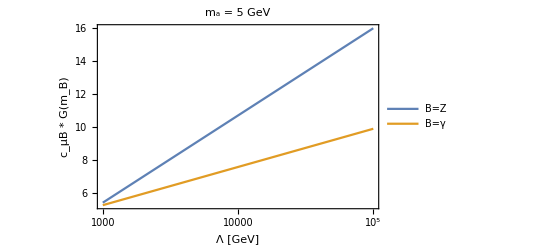

```mathematica
LogLinearPlot[{(1/(sw (1-sw^2))I3μ G[Λ,91.2,5])/.{sw-> 0.23142,I3μ-> 1/2},G[Λ,0,5]},{Λ,10^3,10^5},Frame->True,{FrameLabel->{"Λ [GeV]","c_μB * G(m_B)"}},PlotLegends->{"B=Ζ","B=γ"},PlotLabel->"m_a = 5 GeV"]
```

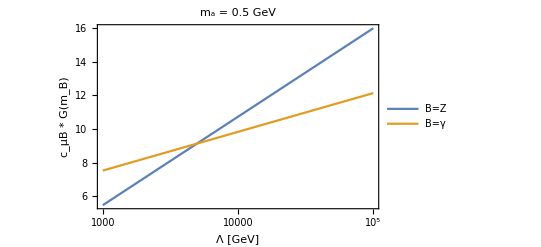

```mathematica
LogLinearPlot[{(1/(sw (1-sw^2))I3μ G[Λ,91.2,0.5])/.{sw-> 0.23142,I3μ-> 1/2},G[Λ,0,0.5]},{Λ,10^3,10^5},Frame->True,{FrameLabel->{"Λ [GeV]","c_μB * G(m_B)"}},PlotLegends->{"B=Ζ","B=γ"},PlotLabel->"m_a = 0.5 GeV"]
```

```mathematica
Block[{Λ=1000},{(1/(sw (1-sw^2))I3μ G[Λ,91.2,5])/.{sw-> 0.23142,I3μ-> 1/2},G[Λ,0,5]}]
```

{5.4467,5.29624}

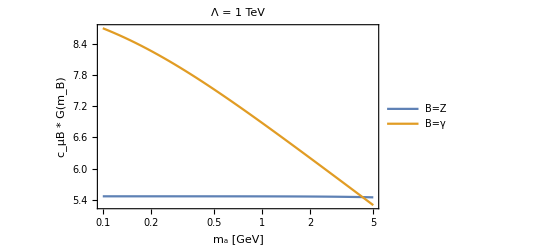

```mathematica
LogLinearPlot[{(1/(sw (1-sw^2))I3μ G[1000,91.2,ma])/.{sw-> 0.23142,I3μ-> 1/2},G[1000,0,ma]},{ma,10^-1,5},Frame->True,{FrameLabel->{"m_a [GeV]","c_μB * G(m_B)"}},PlotLegends->{"B=Ζ","B=γ"},PlotLabel->"Λ = 1 TeV"]
```

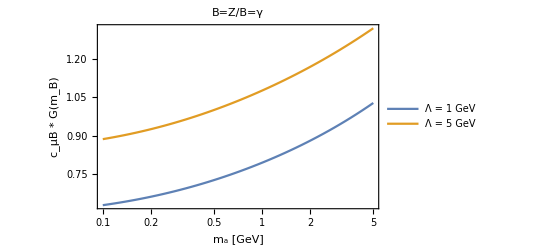

```mathematica
LogLinearPlot[{((1/(sw (1-sw^2))I3μ G[1000,91.2,ma])/.{sw-> 0.23142,I3μ-> 1/2})/G[1000,0,ma],((1/(sw (1-sw^2))I3μ G[5000,91.2,ma])/.{sw-> 0.23142,I3μ-> 1/2})/G[5000,0,ma]},{ma,10^-1,5},Frame->True,{FrameLabel->{"m_a [GeV]","c_μB * G(m_B)"}},PlotLegends->{"Λ = 1 GeV","Λ = 5 GeV"},PlotLabel->"B=Ζ/B=γ"]
```